{{1,-0.5},{-1,2.5},{1-√3,-3.5},{-1+2 √3,2.5},{1-2 √3,-0.5},{-1+3 √3,-0.5},{1-3 √3,2.5},{-1+2 √3,-3.5},{1-√3,2.5},{-1,-3.5},{1+√3,2.5},980,{-1+16 √3,32.5},{1-16 √3,-30.5},{-1+17 √3,29.5},{1-17 √3,-27.5},{-1+18 √3,26.5},{1-18 √3,-24.5},{-1+19 √3,23.5},{1-19 √3,-21.5},{-1+20 √3,20.5},{1-20 √3,-18.5}}
 |  |  |  |

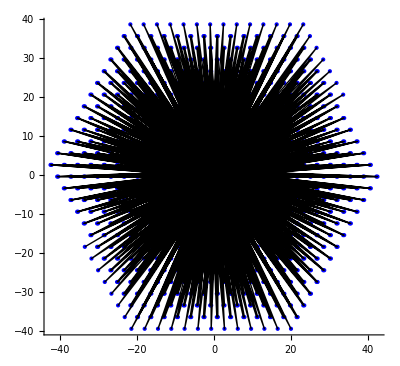

```mathematica
(*-------New Point Calculation-----*)
reflectPoint[outPoint_,middlePoint_]:=(
xMove = -(outPoint[[1]]-middlePoint[[1]]);
yMove=-(outPoint[[2]]-middlePoint[[2]]);
{middlePoint[[1]]+xMove,middlePoint[[2]]+yMove}
)

(*-------Points & Triangle-----*)
xA=0;yA=1; pointA={xA,yA}; textA= Text["A",{0.1,1}];
xB=-(√3)/2;yB=-1/2; pointB={xB,yB}; textB = Text ["B",{-0.92,-0.54}];
xC=(√3)/2; yC=-1/2; pointC={xC,yC}; textC = Text["C",{0.92,-0.54}];
triangle1=Polygon[CirclePoints[3]];
(*---equations[P&T]---*)
h[x_]:=1+Sqrt[3]*x;
g[x_]:=1-Sqrt[3]*x;
f:=-0.5;

(*-------Initialisation Point [START]--------*)
xK=1;yK=-0.5;
n=1000;


pointK={xK,yK}; textK=Text["K",{xK+0.1,yK+0.1}];
(*------Inner Triangle Check-------*)
If[yK<h[xK]&&yK<g[xK]&&yK>f,
Goto[end];
]

(*------Pointlist Create-------*)
pointList={pointK};
Do[
xP=First[Last[pointList]];
yP=Last[Last[pointList]];
If[yP<h[xP]&& yP>=g[xP],
AppendTo[pointList,reflectPoint[Last[pointList],pointA]]];
If [yP>=h[xP]&& yP>f,
AppendTo[pointList,reflectPoint[Last[pointList],pointB]]];
If [yP<g[xP]&& yP<=f,
AppendTo[pointList,reflectPoint[Last[pointList],pointC]]];
,n];

Label[end];
(*----------Test Output----------*)
plot2={EdgeForm[Directive[Thick,Blue]],Directive[White],triangle1,Directive[Black],Point[pointA],Point[pointB],Point[pointC],textA,textB,textC,PointSize[0.02],Point[pointK],textK};
plot3={Blue,Point[pointList],Black,Line[pointList]};
plot4={plot2,plot3};
pointList
Show[Graphics[plot4],Axes-> True,AxesStyle->Black]
```